```mathematica
Manipulate[Plot[{x^2/2+β x^4/4,x^2/2,β x^4/4},{x,-2,2}],{β,-2,2}]
```

```mathematica
Series[Cos[x],{x,0,8}]
```

1-x^2/2+x^4/24-x^6/720+x^8/40320+O[x]^9

```mathematica
Labels={"x^2/2-x^4/24+x^6/720",
"x^2/2",
"x^2/2-x^4/24",
"-x^4/24+x^6/720",
"1-Cos[x]"};
```

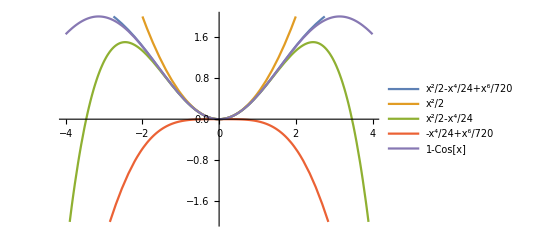

```mathematica
Plot[
{x^2/2-x^4/24+x^6/720,
x^2/2,
x^2/2-x^4/24,
-x^4/24+x^6/720,
1-Cos[x]},{x,-4,4},PlotRange->{-2,2},PlotLegends->Labels]
```

```mathematica
U[x_,r_]:=(1-Cos[x])/r
```

```mathematica
U[x,1]+U[x,2]+U[x,3]
```

1+5/6 (1-Cos[x])-Cos[x]

```mathematica
RandomReal[]
```

0.427507

```mathematica
tablita=Table[
x1=2*(RandomReal[]-0.5);
x2=2*(RandomReal[]-0.5);
x3=2*(RandomReal[]-0.5);
x4=2*(RandomReal[]-0.5);
n=0;
{x1,x2(*+x2+x3+x4*),U[x1,1^n]+U[x2,2^n](*+U[x3,3^n]+U[x4,4^n]*)}
,{i,1,1000}];
(*aaa=ListPlot[tablita]*)
ListPointPlot3D[tablita]
```

-Graphics3D-

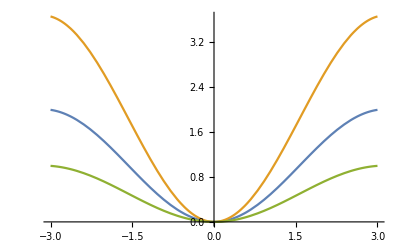

```mathematica
bbb=Plot[{1-Cos[x],1+5/6 (1-Cos[x])-Cos[x],U[x,1]-U[x,2]},{x,-3,3}]
```

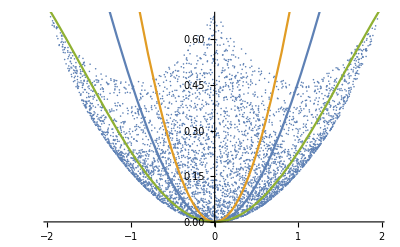

```mathematica
Show[{aaa,bbb}]
```

```mathematica
√0.2
```

0.447214

```mathematica
Ep[x_,r_,α_]:=(1-Cos[x])/r^α
```

```mathematica
Ep[aa,1,1]
```

{0.00111242,0.193221,0.0854312,0.00214666,0.418386,0.00157243,0.381164,0.0678972,0.00585512,0.426601}

```mathematica
Npart=20;
alpha=1;
θ=π; (*Between -π and π *)
x=2θ RandomReal[{0,1},Npart] -θ;
Pot[i_,j_,alpha_]:=Ep[x[[i]] -x[[j]],Abs[i-j],alpha];
Ept[i_,Npart_,alpha_]:=(∑_(j=1)^(i-1) Pot[i,j,alpha]+∑_(j=i+1)^Npart Pot[i,j,alpha]);
Ept[Npart/2,Npart,alpha]
```

5.0886

```mathematica
Ep[x_,r_,α_]:=(1-Cos[x])/r^α
```

Dado una magnetizacion definida M_0 cuanto cambiara la energia y magnetizacion de una particula si la cambio aleatorioamente?

```mathematica
Npart=20;
aleatorios=RandomReal[{0,1},Npart];
```

```mathematica
θ=0.2π;
ϕ=2θ aleatorios -θ;
m = Table[{Cos[ϕ[[i]]],Sin[ϕ[[i]]]},{i,1,Length[ϕ]}];
M = Norm[m]/Npart;
```

```mathematica
Lista04=Table[
m[[1]][[1]]=Cos[a];
m[[1]][[2]] =Sin[a];
{a,(Norm[m]/Npart)-M},{a,-π,π,0.01}];
```

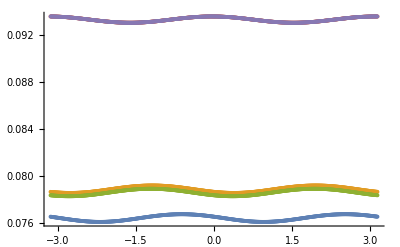

```mathematica
ListPlot[{Lista00,Lista01,Lista02,Lista03,Lista04}]
```

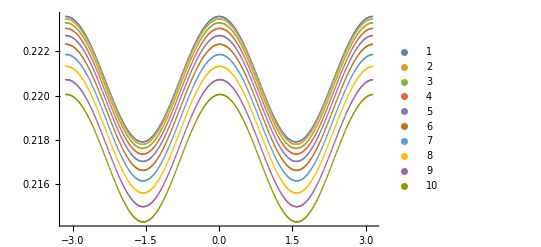

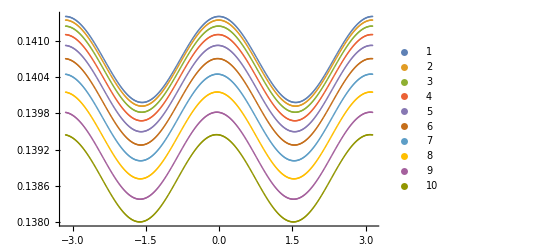

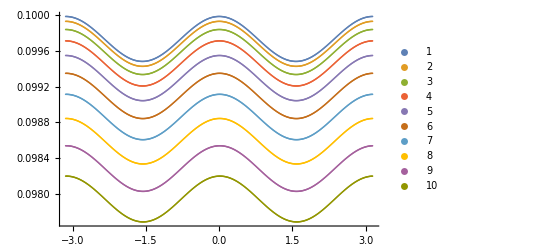

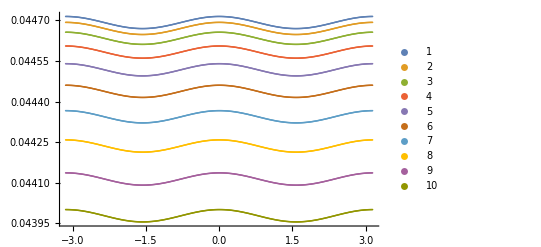

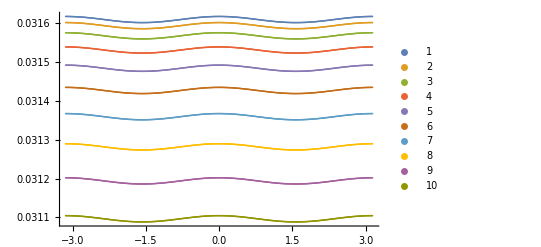

```mathematica
MagAngle=Table[
θ=0.01i π;
ϕ=2θ aleatorios -θ;
m = Table[{Cos[ϕ[[i]]],Sin[ϕ[[i]]]},{i,1,Length[ϕ]}];
M = Norm[m]/Npart;
tablita=Table[
m[[1]][[1]]=Cos[a];
m[[1]][[2]] =Sin[a];
{a,(Norm[m]/Npart)},{a,-π,π,0.01}];
tablita,{i,1,10}
];
ListPlot[MagAngle,PlotLegends->Automatic]
```

Entonces puedo concluir que las fluctuaciones en la magnetizaci[on son del orden de 10^-3

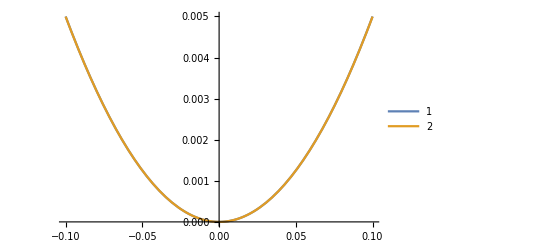

```mathematica
Plot[{x^2/2,1-Cos[x]},{x,-0.1,0.1},PlotLegends->Automatic]
```

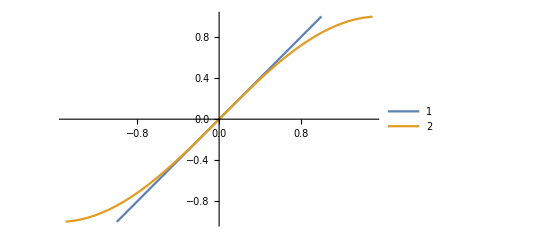

```mathematica
Plot[{x,Sin[x]},{x,-1.5,1.5},PlotRange->{-1,1},PlotLegends->Automatic]
```

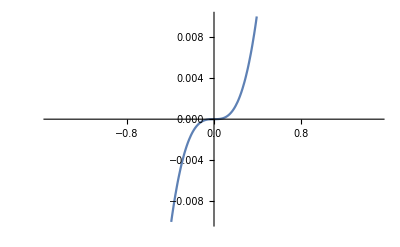

```mathematica
Plot[x-Sin[x],{x,-1.5,1.5},PlotRange->{-0.01,0.01},PlotLegends->Automatic]
```

```mathematica
Manipulate[
Plot[{1,Cos[x]},{x,-a,a},PlotRange->{0,1.2},PlotTheme->"Detailed"]
,{a,2,0.01}]
```

```mathematica
Clear[α]
PotTest[x_,y_]:=1-Cos[x]+(1-Cos[y])
Plot3D[PotTest[x,y],{x,-2π,2π},{y,-2π,2π},PlotTheme->"Detailed"]
```

-Graphics3D-

```mathematica
Plot3D[{x^2+y^2,2-Cos[x]-Cos[y]},{x,-π/2,π/2},{y,-π/2,π/2},PlotTheme->"Scientific"]
```

-Graphics3D-

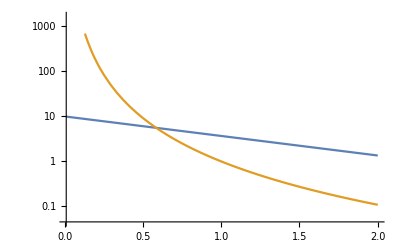

```mathematica
LogPlot[{10 Exp[-1 x],x^-3.2},{x,0.01,2}]
```

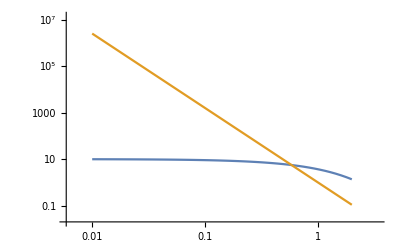

```mathematica
LogLogPlot[{10 Exp[-1 x],x^-3.2},{x,0.01,2}]
```